```mathematica
Needs["Quantum`Computing`"];
```

```mathematica
SetComputingAliases[];
```

```mathematica
Clear[SimonOracle,SimonAlgorithm]
```

The randomized Simon oracle; Simon’s algorithm is shown after.
       a = period
       n = number of qubits

```mathematica
SimonOracle[a_,n_]:=Module[
{B,k,O1,O2,C,O,H},
On[Assert];
If[a>0,Assert[Ceiling[Log2[a]]≤n],
Return [O2=⊗_(j=1)^n(𝒞^{ĵ})[Subscript[𝒩𝒪𝒯, OverHat[j+n]]]]
];
B=Flatten[Position[Reverse[IntegerDigits[a,2,n]],1]];
k=B[[1]];
C=Delete[Range[1,n],k];
If[Length[B]==1,O1=Subscript[ℐ, k̂],O1=⊗_(j=2)^Length[B](𝒞^{k̂})[Subscript[𝒩𝒪𝒯, OverHat[B[[j]]]]];];
O2=⊗_(j=1)^(n-1)(𝒞^{OverHat[C[[j]]]})[Subscript[𝒩𝒪𝒯, OverHat[C[[j]]+n]]];
H=Subscript[ℋ, OverHat[k+n]];
Return[ExpandAll[H·O1·O2·O1]];
]
```

```mathematica
SimonAlgorithm[a_,n_]:=QubitMeasurement[Subscript[ℋ, Range[1,n]]·SimonOracle[a,n]·Subscript[ℋ, Range[1,n]]·(|0⟩)_(2n),Table[k̂,{k,1,n}]]
```

Simon algorithm for 2 qubits

Probability | Measurement | State
1/4 | (0_1 | 0_2) | |0⟩⊗|0⟩⊗(|0⟩+|1⟩)⊗((|0⟩)/2+(|1⟩)/2)
1/4 | (0_1 | 1_2) | |0⟩⊗|1⟩⊗(|0⟩+|1⟩)⊗((|0⟩)/2-(|1⟩)/2)
1/4 | (1_1 | 0_2) | |1⟩⊗|0⟩⊗(|0⟩-|1⟩)⊗((|0⟩)/2+(|1⟩)/2)
1/4 | (1_1 | 1_2) | |1⟩⊗|1⟩⊗(|0⟩-|1⟩)⊗((|0⟩)/2-(|1⟩)/2)
Probability | Measurement | State
Probability | Measurement | State
1/2 | (0_1 | 0_2) | |0⟩⊗|0⟩⊗(|0⟩+|1⟩)⊗((|0⟩)/2+(|1⟩)/2)
1/2 | (0_1 | 1_2) | |0⟩⊗|1⟩⊗(|0⟩+|1⟩)⊗((|0⟩)/2-(|1⟩)/2)
Probability | Measurement | State
Probability | Measurement | State
1/2 | (0_1 | 0_2) | |0⟩⊗|0⟩⊗(|0⟩+|1⟩)⊗((|0⟩)/2+(|1⟩)/2)
1/2 | (1_1 | 0_2) | |1⟩⊗|0⟩⊗(|0⟩-|1⟩)⊗((|0⟩)/2+(|1⟩)/2)
Probability | Measurement | State
Probability | Measurement | State
1/2 | (0_1 | 0_2) | |0⟩⊗|0⟩⊗(|0⟩+|1⟩)⊗((|0⟩)/2+(|1⟩)/2)
1/2 | (1_1 | 1_2) | |1⟩⊗|1⟩⊗(|0⟩+|1⟩)⊗((|0⟩)/2-(|1⟩)/2)
Probability | Measurement | State

Instractable Simon oracles for 2 qubits

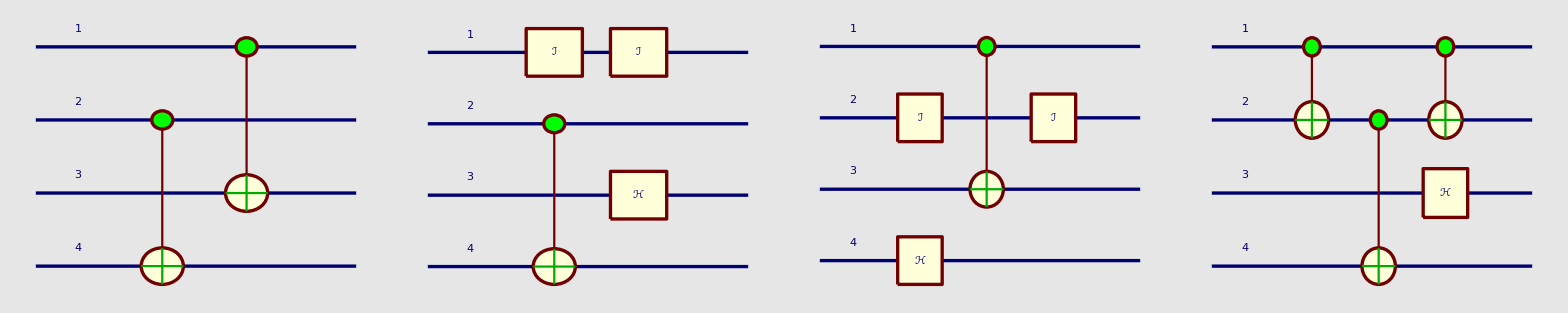

```mathematica
n=2;
Print["Simon algorithm for ",n," qubits"]
Partition[TraditionalForm[QuantumEvaluate[SimonAlgorithm[#,n]]]&/@ Range[0,2^n-1],UpTo[n/2]]//Grid
Print["Instractable Simon oracles for ",n," qubits"]
Partition[QuantumPlot[SimonOracle[#,n]]&/@ Range[0,2^n-1],UpTo[2n]]//Grid
```

Simon algorithm for 3 qubits

Probability | Measurement | State
1/8 | (0_1 | 0_2 | 0_3) | |0⟩⊗|0⟩⊗|0⟩⊗(|0⟩+|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
1/8 | (0_1 | 0_2 | 1_3) | |0⟩⊗|0⟩⊗|1⟩⊗(|0⟩+|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)-(|1⟩)/(2 √2))
1/8 | (0_1 | 1_2 | 0_3) | |0⟩⊗|1⟩⊗|0⟩⊗(|0⟩+|1⟩)⊗(|0⟩-|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
1/8 | (0_1 | 1_2 | 1_3) | |0⟩⊗|1⟩⊗|1⟩⊗(|0⟩+|1⟩)⊗(|0⟩-|1⟩)⊗((|0⟩)/(2 √2)-(|1⟩)/(2 √2))
1/8 | (1_1 | 0_2 | 0_3) | |1⟩⊗|0⟩⊗|0⟩⊗(|0⟩-|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
1/8 | (1_1 | 0_2 | 1_3) | |1⟩⊗|0⟩⊗|1⟩⊗(|0⟩-|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)-(|1⟩)/(2 √2))
1/8 | (1_1 | 1_2 | 0_3) | |1⟩⊗|1⟩⊗|0⟩⊗(|0⟩-|1⟩)⊗(|0⟩-|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
1/8 | (1_1 | 1_2 | 1_3) | |1⟩⊗|1⟩⊗|1⟩⊗(|0⟩-|1⟩)⊗(|0⟩-|1⟩)⊗((|0⟩)/(2 √2)-(|1⟩)/(2 √2))
Probability | Measurement | State
Probability | Measurement | State
1/4 | (0_1 | 0_2 | 0_3) | |0⟩⊗|0⟩⊗|0⟩⊗(|0⟩+|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
1/4 | (0_1 | 0_2 | 1_3) | |0⟩⊗|0⟩⊗|1⟩⊗(|0⟩+|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)-(|1⟩)/(2 √2))
1/4 | (0_1 | 1_2 | 0_3) | |0⟩⊗|1⟩⊗|0⟩⊗(|0⟩+|1⟩)⊗(|0⟩-|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
1/4 | (0_1 | 1_2 | 1_3) | |0⟩⊗|1⟩⊗|1⟩⊗(|0⟩+|1⟩)⊗(|0⟩-|1⟩)⊗((|0⟩)/(2 √2)-(|1⟩)/(2 √2))
Probability | Measurement | State
Probability | Measurement | State
1/4 | (0_1 | 0_2 | 0_3) | |0⟩⊗|0⟩⊗|0⟩⊗(|0⟩+|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
1/4 | (0_1 | 0_2 | 1_3) | |0⟩⊗|0⟩⊗|1⟩⊗(|0⟩+|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)-(|1⟩)/(2 √2))
1/4 | (1_1 | 0_2 | 0_3) | |1⟩⊗|0⟩⊗|0⟩⊗(|0⟩-|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
1/4 | (1_1 | 0_2 | 1_3) | |1⟩⊗|0⟩⊗|1⟩⊗(|0⟩-|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)-(|1⟩)/(2 √2))
Probability | Measurement | State
Probability | Measurement | State
1/4 | (0_1 | 0_2 | 0_3) | |0⟩⊗|0⟩⊗|0⟩⊗(|0⟩+|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
1/4 | (0_1 | 0_2 | 1_3) | |0⟩⊗|0⟩⊗|1⟩⊗(|0⟩+|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)-(|1⟩)/(2 √2))
1/4 | (1_1 | 1_2 | 0_3) | |1⟩⊗|1⟩⊗|0⟩⊗(|0⟩+|1⟩)⊗(|0⟩-|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
1/4 | (1_1 | 1_2 | 1_3) | |1⟩⊗|1⟩⊗|1⟩⊗(|0⟩+|1⟩)⊗(|0⟩-|1⟩)⊗((|0⟩)/(2 √2)-(|1⟩)/(2 √2))
Probability | Measurement | State
Probability | Measurement | State
1/4 | (0_1 | 0_2 | 0_3) | |0⟩⊗|0⟩⊗|0⟩⊗(|0⟩+|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
1/4 | (0_1 | 1_2 | 0_3) | |0⟩⊗|1⟩⊗|0⟩⊗(|0⟩+|1⟩)⊗(|0⟩-|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
1/4 | (1_1 | 0_2 | 0_3) | |1⟩⊗|0⟩⊗|0⟩⊗(|0⟩-|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
1/4 | (1_1 | 1_2 | 0_3) | |1⟩⊗|1⟩⊗|0⟩⊗(|0⟩-|1⟩)⊗(|0⟩-|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
Probability | Measurement | State
Probability | Measurement | State
1/4 | (0_1 | 0_2 | 0_3) | |0⟩⊗|0⟩⊗|0⟩⊗(|0⟩+|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
1/4 | (0_1 | 1_2 | 0_3) | |0⟩⊗|1⟩⊗|0⟩⊗(|0⟩+|1⟩)⊗(|0⟩-|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
1/4 | (1_1 | 0_2 | 1_3) | |1⟩⊗|0⟩⊗|1⟩⊗(|0⟩+|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)-(|1⟩)/(2 √2))
1/4 | (1_1 | 1_2 | 1_3) | |1⟩⊗|1⟩⊗|1⟩⊗(|0⟩+|1⟩)⊗(|0⟩-|1⟩)⊗((|0⟩)/(2 √2)-(|1⟩)/(2 √2))
Probability | Measurement | State
Probability | Measurement | State
1/4 | (0_1 | 0_2 | 0_3) | |0⟩⊗|0⟩⊗|0⟩⊗(|0⟩+|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
1/4 | (0_1 | 1_2 | 1_3) | |0⟩⊗|1⟩⊗|1⟩⊗(|0⟩+|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)-(|1⟩)/(2 √2))
1/4 | (1_1 | 0_2 | 0_3) | |1⟩⊗|0⟩⊗|0⟩⊗(|0⟩-|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
1/4 | (1_1 | 1_2 | 1_3) | |1⟩⊗|1⟩⊗|1⟩⊗(|0⟩-|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)-(|1⟩)/(2 √2))
Probability | Measurement | State
Probability | Measurement | State
1/4 | (0_1 | 0_2 | 0_3) | |0⟩⊗|0⟩⊗|0⟩⊗(|0⟩+|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
1/4 | (0_1 | 1_2 | 1_3) | |0⟩⊗|1⟩⊗|1⟩⊗(|0⟩+|1⟩)⊗(|0⟩-|1⟩)⊗((|0⟩)/(2 √2)-(|1⟩)/(2 √2))
1/4 | (1_1 | 0_2 | 1_3) | |1⟩⊗|0⟩⊗|1⟩⊗(|0⟩+|1⟩)⊗(|0⟩+|1⟩)⊗((|0⟩)/(2 √2)-(|1⟩)/(2 √2))
1/4 | (1_1 | 1_2 | 0_3) | |1⟩⊗|1⟩⊗|0⟩⊗(|0⟩+|1⟩)⊗(|0⟩-|1⟩)⊗((|0⟩)/(2 √2)+(|1⟩)/(2 √2))
Probability | Measurement | State

Instractable Simon oracles for 3 qubits

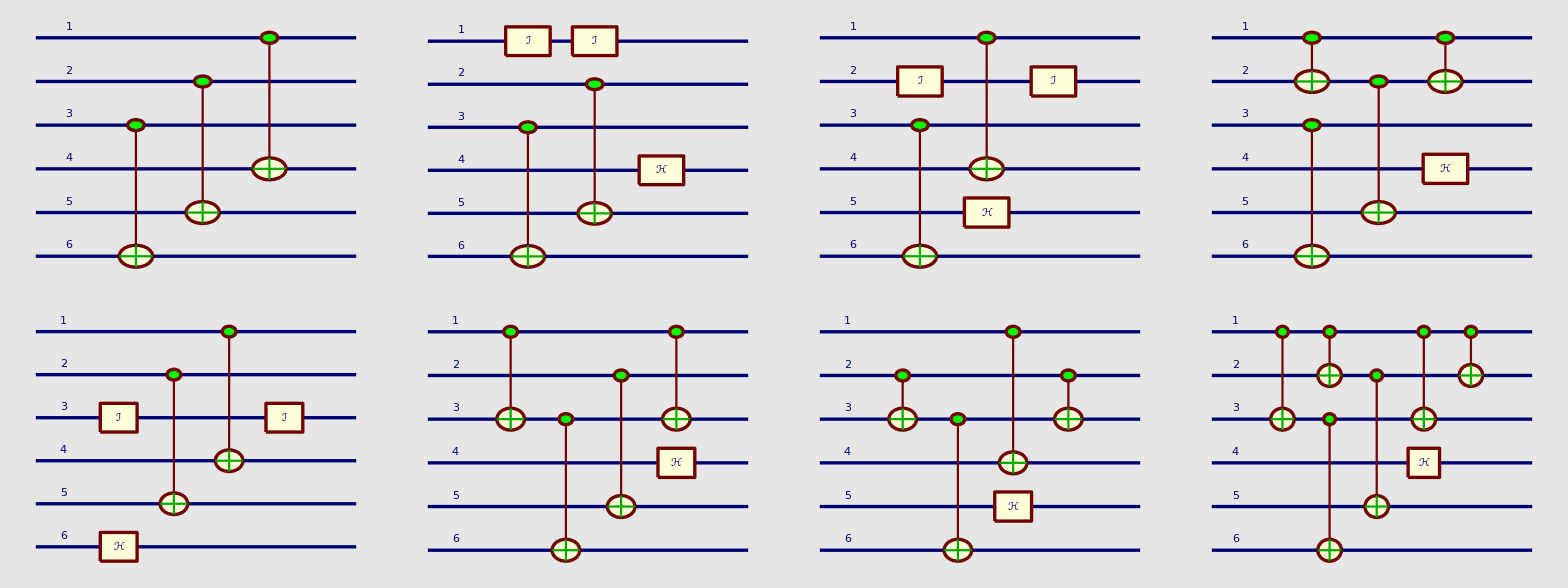

```mathematica
n=3;
Print["Simon algorithm for ",n," qubits"]
Partition[TraditionalForm[QuantumEvaluate[SimonAlgorithm[#,n]]]&/@ Range[0,2^n-1],UpTo[1]]//Grid
Print["Instractable Simon oracles for ",n," qubits"]
Partition[QuantumPlot[SimonOracle[#,n]]&/@ Range[0,2^n-1],UpTo[4]]//Grid
```